# Lab #1 - Exercises

## Exercises

### Problem 1: Typesetting Mathematics within Text using Mathematica

One of the objectives of our Calculus II course is for students to become more effective communicators in the area of technical writing. The Mathematica labs are the environment where you will be able to practice your technical writing skills. With a bit of practice you can learn how to embed mathematical expressions into text cells to produce very nice looking documents.

In this first assignment you are just asked to typeset some text containing mathematics along with English words. In particular you are required to type the statemnt of the Inverse Function Theorem found on page 308 of our text book in the box labelled with the number 7 and part of its proof. For your convenenience a .pdf of the statement of the theorem and its proof are provided on blackboard.

type the statemnt of the Inverse Function Theorem found on page 308 of our text book (and page 389 of the e-book) in the box labelled with the number 7.

type the first paragraph of the proof of this theorem, ending with “y→b. Therefore”

(Bonus) Type in the remainder of the proof which ends at the bottom of page 308.

You may find the following key board short cuts worth committing to memory.

When you begin a new cell in Mathematica (prior to typing anything) Alt-7 makes the cell a Text cell. (You can also click on the plus symbol that you see when you are about to start a new cell and select the type of cell you want).

While typing in a text cell Ctrl-9 begins an embeded math expression and Ctrl-0 ends the embedded expression

While working in a math cell  the arrow key ⟶ moves the "level" of the cursor.

Theorem: If f is a one-to-one differentiable function, with inverse function f^-1 and f'(f^-1(a))≠0, then the inverse function is differentiable at a, and:

(f^-1)'(a)=1/(f'(f^-1(a)))

Proof: Write the definition of derivative as in Equation 2.1.5:

(f^-1)'(a)=lim_(x→a) (f^-1(x)-f^-1(a))/(x-a)

If f(b)=a, then f^-1(a)=b. And if we let y=f^-1(x), then f(y)=x. Since f is differentiable, it is continuous, so f^-1 by Theorem 6. Thus, if x→a, …

### Problem 2: Solving a difficult equation with Mathematica

The goal of this exercise is to find real solutions to the equation 2^x= x^8 .

Use the Solve command to get Mathematica to solve this equation.

Mathematica's output (after it gives some warning messages) should be a list of 9 exact solutions each of which is described in terms of a function that you probably have never heard of before called ProductLog.

Use Mathematica's built in help feature to find out what the definition of this ProductLog function is. Write down this definition in your Mathematica notebook (i.e., what you submit).

Investigate each of the 9 solutions Mathematica produced by using the N command along with the rules replacement command /. as was done in the discussion earlier in this lab.

Find all of the solutions to this equation which are real numbers. Give 10 digits of accuracy for each of these solutions. [Hint: Use the built in help feature to learn about some optional inputs to Solve and N.]

```mathematica
Solve[2^x==x^8,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-(8 ProductLog[-Log[2]/8])/Log[2]},{x→-(8 ProductLog[-1/8 ⅈ Log[2]])/Log[2]},{x→-(8 ProductLog[1/8 ⅈ Log[2]])/Log[2]},{x→-(8 ProductLog[Log[2]/8])/Log[2]},{x→-(8 ProductLog[-1/8 (-1)^(1/4) Log[2]])/Log[2]},{x→-(8 ProductLog[1/8 (-1)^(1/4) Log[2]])/Log[2]},{x→-(8 ProductLog[-1/8 (-1)^(3/4) Log[2]])/Log[2]},{x→-(8 ProductLog[1/8 (-1)^(3/4) Log[2]])/Log[2]},{x→-(8 ProductLog[-1,-Log[2]/8])/Log[2]}}

ProductLog[z]:
	gives the principal solution for w in z==w e^w.

```mathematica
Solve[2^x==x^8,x] ~N~ 10
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1.09999703},{x→-0.0849597956+0.9890233906 ⅈ},{x→-0.0849597956-0.9890233906 ⅈ},{x→-0.9231317862},{x→0.697211409+0.8014457204 ⅈ},{x→-0.700676609-0.628264244 ⅈ},{x→-0.700676609+0.628264244 ⅈ},{x→0.697211409-0.8014457204 ⅈ},{x→43.55926044}}

### Problem 3: The denisity of the prime numbers

This problem corresponds to homework problem #74 in section 6.3 of our e-text (see page 410) which says (with a slight notational change):

"A prime number is a positive integer that has no factors other than 1 and itself. The first few primes are 2, 3, 5, 7, 11, 13, 17, ... . We denote by p(n) the number of primes that are less than or equal to n. For instance p(15) = 6 because there are six primes smaller than 15. 
	(a) Calculate p(25)  and p(100) 
	(b) By inspecting tables of prime numbers and tables of logarithms, the great Mathematician K.F. Gauss made the guess in 1792 (when he was 15) that the number of primes up to n is approximately n/(ln (n)) when n is large. More precisely, he conjectured that 
				lim_(n → ∞) (p(n))/(n / ln(n))= 1
This was finally proved, a hundred years later by Jaques Hadamard and Charles de la Vallée and is called the Prime Number Theorem. Provide evidence for the truth of this theorem by computing the ratio of p(n) to n/ln(n) for n = 100, 1000, 10^4, 10^5, 10^6, 10^7. Use the following data: p(1000) = 168, p(10^4) = 1229 , p(10^5) = 9592 , p(10^6) = 78,498 , p(10^7) = 664,579 . 
	(c) Use the Prime Number Theorem to estimate the number of primes up to a billion."

In this problem you are asked to define the function p(n) using Mathematica

Hint: Your function can be built using the following Mathematica commands: PrimeQ, If, Table, and Total

Extended Hint:  The function "PrimeQ" returns a value of True or False, use the "If" command to convert this output to a 1 if the value was true and a 0 if the value was false. Mathematica's ability to work with lists allows very powerful commands to be constructed by a single line of code. Build a list of 0's and 1's by using the "Table" command, and then find the Total of number of the entries in this list. This can all be done in a single line by nesting these functions. Build this in steps, get the inner nested functions working before you put it all together in one line of Mathematica code. But before trying to get a concise answer, experiment with each of the commands to make sure you understand them.

Verify the values of p(n) given in the statement of the homework problem are equal to the values computed by your function p(n). Note that computing the value of p(10^7) may take Mathematica a minute or two.

Answer part (c) of the homework problem. You should do this by using the Prime Number Theorem, not by getting Mathematica to calculate p(1,000,000,000) which would take a long time. Explain your reasoning.

```mathematica
p[n_]:=Total[Table[If[PrimeQ[i],1,0],{i, n}]]
```

```mathematica
p[10^#]&/@Range[2,7]
```

{25,168,1229,9592,78498,664579}

```mathematica
1000000000/Log[1000000000]//N
```

4.82549×10^7

I applied Gauss’s conjecture that one can number the primes up to n by applying n/(ln (n)), substituting 1,000,000,000 for n.

### Problem 4: The Curious Expression, (1+1/x)^x

This exercise corresponds to the discussion at the end of section 6.4 of the text.

As x→ ∞, the base of the expression  (1+1/x)^x goes to 1, while the exponent goes to infinity. For short, people often write this as saying the limit of the expression has the form of " 1^∞ ", this is an "indeterminate form," which is to say that the value of the limit of  (1+1/x)^x as x→ ∞ is not obvious. Is the limit 1? Does the limit go to infinity? How does the limit change if we change the base to something like (1+(ln 2)/x) ? Investigate this expression. Your answer should include:

A plot of (1+1/x)^x that includes a large enough value for x to show that the limit is most likely not 1.

An evaluation of the limit of (1+1/x)^x as x→ ∞.

An evaluation of the limit of (1+(ln 2)/x)^xas x→ ∞.

A conjecture as to the value of the limit of (1+c/x)^x as x→ ∞.

Useful commands for this exercise are Plot and Limit

```mathematica
c[x_]:=(1+1/x)^x
```

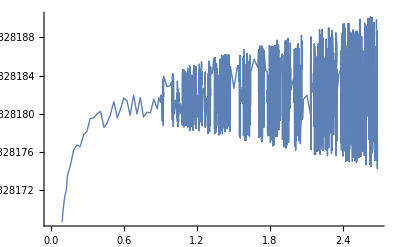

```mathematica
Plot[c[x],{x,0,2^28},PlotStyle->Thin]
```

```mathematica
Limit[(1+1/x)^x,x->∞]
```

ⅇ

```mathematica
Limit[(1+Log[2]/x)^x,x->∞]
```

2

```mathematica
Limit[(1+2/x)^x,x->∞]
```

ⅇ^2

Well, it looks like it’s going to whatever’s in the denominator is going to end up being the power of ⅇ. Sooooo,

```mathematica
Limit[(1+c/x)^x,x->∞]
```

ⅇ^c

```mathematica
lim_(x->∞) ⅇ^(log((2/x+1)^x))=lim_(x->∞) ⅇ^(x·log(2/x+1))=ⅇ^(lim_(x->∞) x·log(2/x+1))…
```